## Parameters

```mathematica
(*These parameters are caught from CI*)
mg=0.8;αir=0.93π;Λir=0.24;Λuv=0.905;
mu=0.007;
τir=1/Λir;τuv=1/Λuv;
(*T from 0.01 to 0.3 ,0.01 every step*)
start=0.01;end=0.30;step=0.01;
T=Table[x,{x,start,end,step}];
M=Table[0,{30}];
(*Error range*)ϵ=0.000001;
```

## Function

```mathematica
(*This function is similar to CI function C, also named Ϛ,but in different form*)
Ϛ[M_,T_]:=T*NIntegrate[(E^(-τ*M^2))/τ^(3/2)EllipticTheta[2,0,E^(-4τ*π^2*T^2)],{τ,τuv^2,τir^2}];
Mass[M_,T_]:=mu+M*(8*αir)/(3Sqrt[π]*mg^2)*Ϛ[M,T];
```

## Calculate

```mathematica
(*Calculation, every Ti give Mi*)

(*Parallelize calculation*)
CloseKernels[];
LaunchKernels[16];
SetSharedVariable[M];
ParallelDo[
	T0=T[[i]];
	M0=0;(*Initial value*)
	M1=0.35;(*Initial value*)
	(*Calculation, DS equation*)
		While[
		Abs[M1-M0]>ϵ,
		M0=M1;
		M1=Mass[M0,T0];
		];
	M[[i]]=M1
	,
	{i,Length[T]}
]

(*
Do[
Print[M[[i]]],
{i,Length[M]}
]
*)
```

## Draw Chart

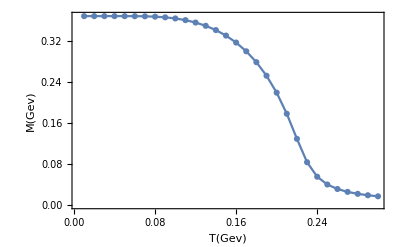

```mathematica
(*Draw chart*)
Chart=ListLinePlot[
Transpose[{T,M}],
PlotMarkers->Automatic,
Frame->True,
FrameLabel->{Style["T(Gev)",Bold,12.5],Style["M(Gev)",Bold,12.5]},
PlotRange->Full
]
```

## Export Result

```mathematica
Export["E:\\NJU\\program\\Infinite_temprature\\Result_pdf\\zero_miu_quark_mass.pdf",Chart];
```